```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=20;
Ly=20;
A=Lx*Ly;
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2,sx2d[j+1+k Lx,j+k Lx]=I/2},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2,sx2dp[1+k Lx,(k+1)Lx]=I/2},{k,0,Ly-1}]

SX2DP=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2,cx2d[j+1+k Lx,j+k Lx]=1/2},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2,cx2dp[1+k Lx,(1+k)Lx]=1/2},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHI]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHI[1.0,1.0,1.5,0.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

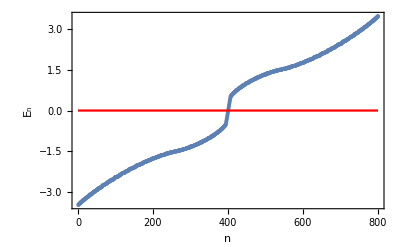

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],Plot[0,{x,0,2A},PlotStyle-> Red],BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
InvH=Inverse[HamiltonianQAHI[1.0,1.0,3.0,1.0]];
```

```mathematica
value=Eigenvalues[InvH];
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------- Computation of Bott Index -----------------*)
```

```mathematica
Clear[vecNormalized,ValVecNor,U,Ux,Vy,U,V,P,LogEigenValuesBott,Bott,BottIndex]
```

```mathematica
vecNormalized=Table[Normalize[vec[[i]]],{i,1,2 A}];
```

```mathematica
ValVecNor=SortBy[Transpose[{val,vecNormalized}],First];
```

```mathematica
FilledEigenvectors=Table[ValVecNor[[i]][[2]], {i,1,A}];
```

```mathematica
Clear[P]
P=Table[0,{i,1,2A},{j,1,2A}];
```

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, A}];
```

```mathematica
XList = Flatten[Transpose[Table[i,{i,1,Lx},{j,1,Ly}]]];
```

```mathematica
YList = Flatten[Table[i,{i,1,Lx},{j,1,Ly}]];
```

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
U = P . Ux. P + IdentityMatrix[2 A] - P;
```

```mathematica
V = P . Vy . P + IdentityMatrix[2A] - P;
```

```mathematica
Bott = U.V.ConjugateTranspose[U].ConjugateTranspose[V];
```

```mathematica
LogEigenValuesBott=Log[Eigenvalues[Bott]];
```

```mathematica
BottIndex = Re[(I/(2π))Total[LogEigenValuesBott]]
```

-1.

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

800

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+16
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-1
```

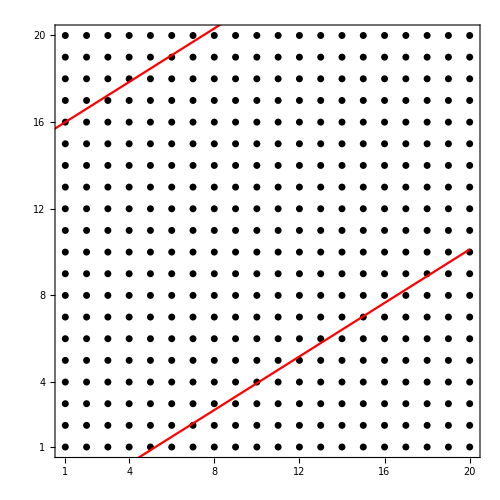

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,20.1},{0.9,20.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[((1+√5)/2)^-1*(x-1)+16,{x,0,Lx},PlotStyle-> Red],
Plot[((1+√5)/2)^-1*(x-2)-1,{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy, P,U,V,LogEigenValuesBott,Bott, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Ly],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
Fibonup=Sort[FibonupNew]
```

{1,2,3,4,5,21,22,23,24,25,26,41,42,43,44,45,46,47,48,61,62,63,64,65,66,67,68,69,70,81,82,83,84,85,86,87,88,89,90,91,101,102,103,104,105,106,107,108,109,110,111,112,113,121,122,123,124,125,126,127,128,129,130,131,132,133,134,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,388,389,390,391,392,393,394,395,396,397,398,399,400}

```mathematica
YList = Ceiling[Fibonup/Lx];
```

```mathematica
XList = Fibonup - (YList - 1)Lx;
```

```mathematica
(**Check**)
```

```mathematica
XList + (YList-1)*Lx - Fibonup
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
Fibondown=Table[Fibonup[[j]]+A,{j,1,Dimensions[Fibonup][[1]]}];
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

602

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

198

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
]
```

```mathematica
Dimensions[a]
```

{198}

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHI[1.,1.,1.5,0.];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon,OnlyEigenvalue]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
(**------Check that HFibonRenor is Hermitian------**)
```

```mathematica
(**--- ConjugateTranspose[HFibonRenor] - HFibonRenor//Chop ---**)
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

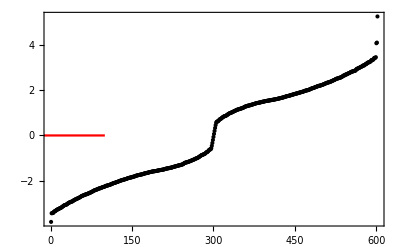

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black],Plot[0,{x,-100,100},PlotStyle-> Red]]
```

```mathematica
OnlyEigenvalue=Table[ValFibon[[j,2]],{j,1,NOrbitalsQuasi}];
```

```mathematica
Tr[OnlyEigenvalue]//Chop
```

8.37793

```mathematica
(**---- Calculation of Bott Index of the quasicrystal ----**)
```

```mathematica
FilledEigenvectors=Table[ValVecFibon[[i]][[2]], {i,1,NOrbitalsQuasi/2}];
```

```mathematica
P = Table[0,{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
Do[P+=TensorProduct[FilledEigenvectors[[i]] ,Conjugate[ FilledEigenvectors[[i]]]],{i, 1, NOrbitalsQuasi/2}];
```

```mathematica
Dimensions[P]
```

{602,602}

```mathematica
U = P . Ux . P + IdentityMatrix[NOrbitalsQuasi] - P;
```

```mathematica
V = P . Vy . P + IdentityMatrix[NOrbitalsQuasi] - P;
```

```mathematica
Bott = U.V.ConjugateTranspose[U].ConjugateTranspose[V];
```

```mathematica
LogEigenValuesBott=Log[Eigenvalues[Bott]];
```

```mathematica
BottIndexQuasi = Re[(I/(2π))Total[LogEigenValuesBott]]
```

2.96852×10^-15

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*---------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi/2}]
```

{{1.,0},{1.85065,0},{2.37638,0},{3.22703,0},{3.75276,0},{4.60341,0},{5.45407,0},{5.9798,0},{6.83045,0},{7.6811,0},{8.20683,0},{9.05748,0},{9.58321,0},{10.4339,0},{11.2845,0},{11.8102,0},{12.6609,0},{13.5115,0},{14.0373,0},{14.8879,0},{15.4137,0},{16.2643,0},{17.115,0},{17.6407,0},{18.4913,0},{19.0171,0},{19.8677,0},{20.7184,0},{21.2441,0},{22.0948,0},{22.9454,0},{23.4711,0},{24.3218,0},{24.8475,0},{25.6982,0},{26.5488,0},{27.0746,0},{27.9252,0},{28.4509,0},{29.3016,0},{30.1522,0},{30.678,0},{31.5286,0},{32.3793,0},{32.905,0},{33.7557,0},{34.2814,0},{35.132,0},{35.9827,0},{36.5084,0},{37.3591,0},{38.2097,0},{38.7354,0},{39.5861,0},{40.1118,0},{40.9625,0},{41.8131,0},{42.3389,0},{43.1895,0},{43.7152,0},{44.5659,0},{45.4165,0},{45.9423,0},{46.7929,0},{47.6436,0},{48.1693,0},{49.02,0},{49.5457,0},{50.3963,0},{51.247,0},{51.7727,0},{52.6234,0},{53.1491,0},{53.9998,0},{54.8504,0},{55.3761,0},{56.2268,0},{57.0774,0},{57.6032,0},{58.4538,0},{58.9796,0},{59.8302,0},{60.6809,0},{61.2066,0},{62.0572,0},{62.9079,0},{63.4336,0},{64.2843,0},{64.81,0},{65.6607,0},{66.5113,0},{67.037,0},{67.8877,0},{68.4134,0},{69.2641,0},{70.1147,0},{70.6404,0},{71.4911,0},{72.3418,0},{72.8675,0},{73.7181,0},{74.2439,0},{75.0945,0},{75.9452,0},{76.4709,0},{77.3215,0},{78.1722,0},{78.6979,0},{79.5486,0},{80.0743,0},{80.925,0},{81.7756,0},{82.3013,0},{83.152,0},{83.6777,0},{84.5284,0},{85.379,0},{85.9048,0},{86.7554,0},{87.6061,0},{88.1318,0},{88.9824,0},{89.5082,0},{90.3588,0},{91.2095,0},{91.7352,0},{92.5859,0},{93.1116,0},{93.9622,0},{94.8129,0},{95.3386,0},{96.1893,0},{97.0399,0},{97.5657,0},{98.4163,0},{98.942,0},{99.7927,0},{100.643,0},{101.169,0},{102.02,0},{102.87,0},{103.396,0},{104.247,0},{104.772,0},{105.623,0},{106.474,0},{107.,0},{107.85,0},{108.376,0},{109.227,0},{110.077,0},{110.603,0},{111.454,0},{112.304,0},{112.83,0},{113.681,0},{114.206,0},{115.057,0},{115.908,0},{116.433,0},{117.284,0},{118.135,0},{118.66,0},{119.511,0},{120.037,0},{120.887,0},{121.738,0},{122.264,0},{123.114,0},{123.64,0},{124.491,0},{125.342,0},{125.867,0},{126.718,0},{127.569,0},{128.094,0},{128.945,0},{129.471,0},{130.321,0},{131.172,0},{131.698,0},{132.548,0},{133.074,0},{133.925,0},{134.775,0},{135.301,0},{136.152,0},{137.002,0},{137.528,0},{138.379,0},{138.905,0},{139.755,0},{140.606,0},{141.132,0},{141.982,0},{142.833,0},{143.359,0},{144.209,0},{144.735,0},{145.586,0},{146.436,0},{146.962,0},{147.813,0},{148.338,0},{149.189,0},{150.04,0},{150.565,0},{151.416,0},{152.267,0},{152.792,0},{153.643,0},{154.169,0},{155.019,0},{155.87,0},{156.396,0},{157.247,0},{157.772,0},{158.623,0},{159.474,0},{159.999,0},{160.85,0},{161.701,0},{162.226,0},{163.077,0},{163.603,0},{164.453,0},{165.304,0},{165.83,0},{166.68,0},{167.531,0},{168.057,0},{168.907,0},{169.433,0},{170.284,0},{171.134,0},{171.66,0},{172.511,0},{173.037,0},{173.887,0},{174.738,0},{175.264,0},{176.114,0},{176.965,0},{177.491,0},{178.341,0},{178.867,0},{179.718,0},{180.568,0},{181.094,0},{181.945,0},{182.795,0},{183.321,0},{184.172,0},{184.697,0},{185.548,0},{186.399,0},{186.924,0},{187.775,0},{188.301,0},{189.152,0},{190.002,0},{190.528,0},{191.379,0},{192.229,0},{192.755,0},{193.606,0},{194.131,0},{194.982,0},{195.833,0},{196.358,0},{197.209,0},{197.735,0},{198.585,0},{199.436,0},{199.962,0},{200.812,0},{201.663,0},{202.189,0},{203.039,0},{203.565,0},{204.416,0},{205.266,0},{205.792,0},{206.643,0},{207.494,0},{208.019,0},{208.87,0},{209.396,0},{210.246,0},{211.097,0},{211.623,0},{212.473,0},{212.999,0},{213.85,0},{214.7,0},{215.226,0},{216.077,0},{216.927,0},{217.453,0},{218.304,0},{218.829,0},{219.68,0}}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

220

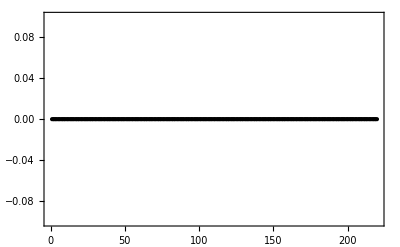

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black]
```

```mathematica
Fibon1D[[3,1]]
```

2.37638

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ValFibon[[(NOrbitalsQuasi/2)+1,2]]
```

0.199014

```mathematica
Clear[J,TabDataFibon,TDFibon,TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabDataFibon=Table[{Fibon1D[[i,1]],0,
Abs[ValVecFibon[[J,2,i]]]^2+Abs[ValVecFibon[[J,2,i+NOrbitalsQuasi/2]]]^2

+Abs[ValVecFibon[[J+1,2,i]]]^2+Abs[ValVecFibon[[J+1,2,i+NOrbitalsQuasi/2]]]^2

},{i,1,NOrbitalsQuasi/2}];
```

```mathematica
TDFibon=Flatten[TabDataFibon];
```

```mathematica
TabFibonacci=Table[{TDFibon[[i]],TDFibon[[i+1]],TDFibon[[i+2]]},{i,1,3*NOrbitalsQuasi/2,3}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,rng,P1]
```

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@TabFibonacci[[All,3]];
```

```mathematica
rng[[2]]
```

0.0332982

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.00"},{rng[[2]]/2,"0.30"},{rng[[2]]-10^-3,"0.60"}}]
```

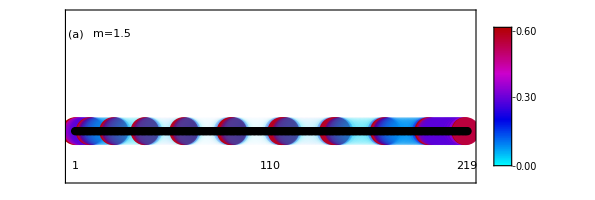

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameTicks-> {None,None},FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.0,largestX},{-3.5,8.5}}],
ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}]
,
Epilog-> {Inset[1,{1,-2.5}],Inset[Ceiling[largestX/2],{Ceiling[largestX/2],-2.5}],Inset[largestX-1,{largestX-1,-2.5}],
Rotate[Inset[P1,{10.5,5.00}],90 Degree],Inset["m=1.5",{21.5,7}],
Inset["(a)",{1.25,7}]
}
]
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ArrayPlot[Re[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
ArrayPlot[Im[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
ArrayPlot[Re[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

-Graphics-

```mathematica
ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {Black,Thick},ColorFunction->"DarkRainbow"]
```

-Graphics-